```mathematica
g=9.8;
l=0.5;
θ0=20*π/180;
ω0=0;

V = 30;
th = .872665;
ode1={x''[t]==(-gx'[t]/vt^2)Sqrt[x'[t]^2+y'[t]^2]};ode2={y''[t]==-g(1+(y'[t]/vt^2)Sqrt[x'[t]^2+y'[t]^2])};sol1=NDSolve[ode1,ode2,x[0]== 0,y[0]==0,x'[0]==VCos[th],y'[0]==VSin[0],{t,0,200}];
```

NDSolve::dsvar: x[0] == 0 cannot be used as a variable.

```mathematica
myplot1 = Plot[(180/Pi) θ[t]/.sol,{t,0,200},PlotStyle-> RGBColor[0,0,1],PlotRange-> All];
omega=√(g/l);
```

ReplaceAll::reps: {sol} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

```mathematica
approx = (180/Pi) θ0 Cos[omega*t];
myplot2=Plot[approx,{t,0,200},PlotStyle-> RGBColor[1,0,0],PlotRange-> All];
```

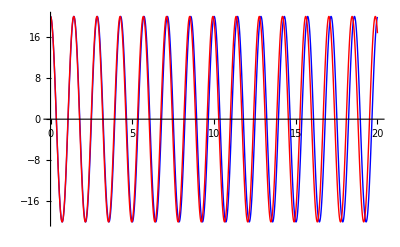

```mathematica
Show[{myplot1,myplot2}]
```

```mathematica
Manipulate[
g=9.8; l=0.5; omega=√(g/l);
Module[
{result = NDSolve[{θ''[t]==-(g/l)*Sin[θ[t]],θ[0]==θ0,θ'[0]==ω0},θ, {t, 0,20}]},
Plot[{(180/Pi) θ0 Cos[omega*t],(180/Pi)* θ[t]/.result},{t,0,20},PlotStyle-> {{Blue},{Dashed,Red}},PlotRange-> All,AxesLabel->{"t (s)","θ (rad)"},PlotRange->{{0,20},{-20,20}},ImageSize->{500,300}]],
{{l,0.5,"length (m)"},0,2,Appearance->"Labeled"},{{θ0,20*Pi/180,"initial angle (rad)"},.1,π/2,Appearance->"Labeled"},
{{ω0,0,"initial speed (rad/s)"},0,10.,Appearance->"Labeled"}]
```